## Patterns and Rules

Паттерн/pattern x_    
Одиночный паттерн (“пустышка”, “Blank”) - любое число, символ, выражение, что угодно

_		Blank[]				бланк 
__		BlankSequence[] 		непустая последовательность бланков
___		BlankNullSequence[]	последовательность бланков

### Blanks

```mathematica
f[x_]:=x+1 (*x_ -> в качестве аргумента всё что угодно*)
```

```mathematica
{f[4],f[a],f["applied maths"]}
```

{5,1+a,1+applied maths}

#### Сходство по типу (_head) (Pattern matching by type)

```mathematica
MatchQ[3.14,_Real] (*Нижнее подчеркивание - является ли*)
```

True

```mathematica
MatchQ[3.14,_Integer]
```

False

```mathematica
Cases[{3,3.14,17,"24",4+5 I},_Integer] (*выбор из списка по образцу - тут только целые*)
```

{3,17}

```mathematica
Cases[{3,3.14,17,"24",4+5 I},_String]
```

{24}

```mathematica
Cases[{g[x],f[x],g[h[x]],g[a,0], f[g[x]]},_g]
```

{g[x],g[h[x]],g[a,0]}

```mathematica
FullForm[g[x]]
```

g[x]

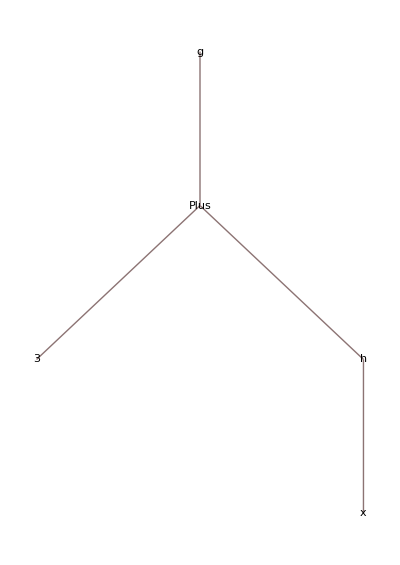

```mathematica
TreeForm[g[h[x]+3]]
```

```mathematica
Cases[{a+b,2+3,"3+4"},_Plus] (* сначала вычислили аргумент функции 2+3, а только потом вызвали Cases*)
```

{a+b}

```mathematica
FullForm[2+3]
```

5

```mathematica
Clear[f]
```

```mathematica
f[x_Integer]:=x+1 (*функция определена только для целых значений аргумента*)
```

```mathematica
{f[-5],f[0],f["5"],f[3.14],f[a]}
```

```mathematica
{f[-5],f[0],f["5"],f[3.14],f[a]}
```

{-4,1,f[5],f[3.14],f[a]}

#### Сходство по структуре (Structured patterns)

```mathematica
Cases[{{a,b},{},{1,0},{c,d,3}},{p_,q_}] (*список из двух элементов*)
```

{{a,b},{1,0}}

```mathematica
Cases[{{a,b},{},{1,0},{c,d,3}},{_,_}] (* тоже самое*)
```

{{a,b},{1,0}}

```mathematica
Cases[{2,9/3,1/3,x/(y+z)},a_/b_]
```

{x/(y+z)}

```mathematica
{FullForm[1/3],FullForm[a/b]}
```

{Rational[1,3],Times[a,Power[b,-1]]}

```mathematica
MatchQ[1/3,Rational[a_,b_]]
```

True

```mathematica
f[{x_,y_}]:=x^2/y^3 (*аргумент - список из 2 элементов!*)
```

```mathematica
{f[{a,b}],f[a,b]} (*список аргументов!*)
```

{a^2/b^3,f[a,b]}

```mathematica
ff[list_List]:=list⟦1⟧^2/list⟦2⟧^3
```

```mathematica
{ff[{a,b}],ff[{a,b,c}]}
```

{a^2/b^3,a^2/b^3}

```mathematica
Clear[f,ff]
```

#### Паттерны для последовательностей (Sequence pattern matching)

Последовательность - выражения, разделённые запятыми. 

__		BlankSequence[] 		непустая последовательность 
___		BlankNullSequence[]		последовательность бланков

```mathematica
MatchQ[{a,b,c,d,e},{p__}] (*это непустой список? проверка на список*)
```

True

```mathematica
MatchQ[{a,b,c,d,e},{__}] (*последовательность непустая?*)
```

True

```mathematica
MatchQ[{a, b, c, d, e},{_}] (*если будет 1 элемент, то True*)
```

True

```mathematica
MatchQ[{Bob},{_}] (*список из одного элемента*)
```

True

```mathematica
Cases[{x,"ab",{},{a},{b,c},{d,e,f}},{___}] (*выбираем списки, в т.ч. пустые*)
```

{{},{a},{b,c},{d,e,f}}

```mathematica
MatchQ[{a,b,c},{___Symbol}](*список из символов*)
```

True

```mathematica
MatchQ[{a,2,c},{___Symbol}]
```

False

```mathematica
MatchQ[{a,b,c},__]
```

True

```mathematica
MatchQ[{},__]
```

True

```mathematica
MatchQ[f[a,b,c],f[x__]]
```

True

```mathematica
(*Tip and Tricks*)
```

```mathematica
Cases[a x^4+b x^3+c x^2+d x+e,(var_)^n_] (*ищет только на первом уровне - поэтому пусто*)
```

{}

```mathematica
(*посмотрим на FullForm*)
```

```mathematica
FullForm[a x^4+b x^3+c x^2+d x+e]
```

Plus[e,Times[d,x],Times[c,Power[x,2]],Times[b,Power[x,3]],Times[a,Power[x,4]]]

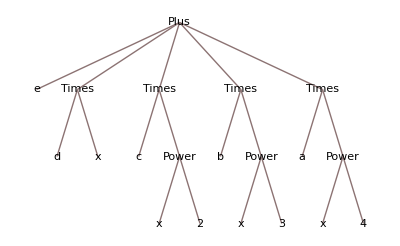

```mathematica
TreeForm[a x^4+b x^3+c x^2+d x+e] (*Power[x,n] только на 3-ем уровне*)
```

```mathematica
Cases[a x^4+b x^3+c x^2+d x+e,(var_)^n_,Infinity] (*искать везде!*)
```

{x^2,x^3,x^4}

#### Условные паттерны (Conditional pattern matching)

expr_ /; test 	- выражение, удовлетворяющее условию
expr_ ?test 	- сокращенная запись

```mathematica
Cases[{1,2,3,4,5,6,7,8,9},n_/;IntegerQ[√n]](*выбрать элементы, которые являются квадратами натуральных чисел*)
```

{1,4,9}

```mathematica
IntegerQ[√21]
```

False

```mathematica
Cases[{x,x^2,x^3,x^4,x^5},_^(n_)/;EvenQ[n]](*элементы в чётной степени*)
```

{x^2,x^4}

Является ли матрица квадратной ?

```mathematica
mat = RandomReal[1,{4,4}];
MatrixForm[mat]
```

(0.341893 | 0.576913 | 0.4374 | 0.640361
0.63936 | 0.0167767 | 0.914116 | 0.982088
0.831631 | 0.83793 | 0.901452 | 0.0500457
0.0193514 | 0.155429 | 0.151997 | 0.645362)

```mathematica
Dimensions[mat]
```

{4,4}

```mathematica
(*напишем функцию для проверки размерности матрицы*)
```

```mathematica
squareMatrixQ[mat_/;MatrixQ[mat]]:=Dimensions[mat]⟦1⟧ ==Dimensions[mat]⟦2⟧ (**)
```

```mathematica
squareMatrixQ[mat]
```

True

```mathematica
squareMatrixQ[RandomReal[1,{3,4}]]
```

False

```mathematica
squareMatrixQ[{{1}}] (*матрица 1х1*)
```

True

```mathematica
(*сокращенная запись*)
```

```mathematica
Cases[{1,2,3,4,5,6,7,8,9},_?PrimeQ]
```

{2,3,5,7}

```mathematica
MatchQ[-Graphics-,_?ImageQ]
```

True

```mathematica
MatchQ[{1,2,3},_List] (*проверяем "голову" выражения*)
```

True

```mathematica
MatchQ[{1,2,3},_?NumberQ] (*является ли, выражение числом*)
```

False

```mathematica
MatchQ[{1,2,3},{__?NumberQ}] (*является ли, выражение списком чисел*)
```

True

```mathematica
(*выбор по критерию*)
```

```mathematica
Cases[{1,2,3,a},_?NumberQ]
```

{1,2,3}

```mathematica
Cases[{-2,7,-1.2,0,-5-2 I},_?Negative]
```

{-2,-1.2}

```mathematica
Table[{2^n-1,2^n+1},{n,0,50}]
```

{{0,2},{1,3},{3,5},{7,9},{15,17},{31,33},{63,65},{127,129},{255,257},{511,513},{1023,1025},{2047,2049},{4095,4097},{8191,8193},{16383,16385},{32767,32769},{65535,65537},{131071,131073},{262143,262145},{524287,524289},{1048575,1048577},{2097151,2097153},{4194303,4194305},{8388607,8388609},{16777215,16777217},{33554431,33554433},{67108863,67108865},{134217727,134217729},{268435455,268435457},{536870911,536870913},{1073741823,1073741825},{2147483647,2147483649},{4294967295,4294967297},{8589934591,8589934593},{17179869183,17179869185},{34359738367,34359738369},{68719476735,68719476737},{137438953471,137438953473},{274877906943,274877906945},{549755813887,549755813889},{1099511627775,1099511627777},{2199023255551,2199023255553},{4398046511103,4398046511105},{8796093022207,8796093022209},{17592186044415,17592186044417},{35184372088831,35184372088833},{70368744177663,70368744177665},{140737488355327,140737488355329},{281474976710655,281474976710657},{562949953421311,562949953421313},{1125899906842623,1125899906842625}}

```mathematica
Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]
```

{0,2,1,3,3,5,7,9,15,17,31,33,63,65,127,129,255,257,511,513,1023,1025,2047,2049,4095,4097,8191,8193,16383,16385,32767,32769,65535,65537,131071,131073,262143,262145,524287,524289,1048575,1048577,2097151,2097153,4194303,4194305,8388607,8388609,16777215,16777217,33554431,33554433,67108863,67108865,134217727,134217729,268435455,268435457,536870911,536870913,1073741823,1073741825,2147483647,2147483649,4294967295,4294967297,8589934591,8589934593,17179869183,17179869185,34359738367,34359738369,68719476735,68719476737,137438953471,137438953473,274877906943,274877906945,549755813887,549755813889,1099511627775,1099511627777,2199023255551,2199023255553,4398046511103,4398046511105,8796093022207,8796093022209,17592186044415,17592186044417,35184372088831,35184372088833,70368744177663,70368744177665,140737488355327,140737488355329,281474976710655,281474976710657,562949953421311,562949953421313,1125899906842623,1125899906842625}

```mathematica
Union[Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]]
```

{0,1,2,3,5,7,9,15,17,31,33,63,65,127,129,255,257,511,513,1023,1025,2047,2049,4095,4097,8191,8193,16383,16385,32767,32769,65535,65537,131071,131073,262143,262145,524287,524289,1048575,1048577,2097151,2097153,4194303,4194305,8388607,8388609,16777215,16777217,33554431,33554433,67108863,67108865,134217727,134217729,268435455,268435457,536870911,536870913,1073741823,1073741825,2147483647,2147483649,4294967295,4294967297,8589934591,8589934593,17179869183,17179869185,34359738367,34359738369,68719476735,68719476737,137438953471,137438953473,274877906943,274877906945,549755813887,549755813889,1099511627775,1099511627777,2199023255551,2199023255553,4398046511103,4398046511105,8796093022207,8796093022209,17592186044415,17592186044417,35184372088831,35184372088833,70368744177663,70368744177665,140737488355327,140737488355329,281474976710655,281474976710657,562949953421311,562949953421313,1125899906842623,1125899906842625}

```mathematica
Cases[Union[Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]],_?PrimeQ] (*выбрать простые числа*)
```

{2,3,5,7,17,31,127,257,8191,65537,131071,524287,2147483647}

```mathematica
Cases[Union[Flatten[Table[{2^n-1,2^n+1},{n,0,50}]]],_?(#1<127&)]
```

{0,1,2,3,5,7,9,15,17,31,33,63,65}

Числа Фибоначчи

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_?IntegerQ]:=fib[n-1]+fib[n-2]
```

```mathematica
{fib[5],fib[10],fib[20],fib[1.2],fib[1+ⅈ]}
```

{5,55,6765,fib[1.2],fib[1+ⅈ]}

```mathematica
fib[-1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
(*ограничим аргумент только натуральными числами*)
```

```mathematica
Clear[fib]
```

```mathematica
fib[1]=fib[2]=1;
```

```mathematica
fib[n_/;IntegerQ[n]&&Positive[n]]:=fib[n-1]+fib[n-2]
```

```mathematica
{fib[5],fib[-10],fib[20],fib[1.2],fib[1+ⅈ]}
```

{5,fib[-10],6765,fib[1.2],fib[1+ⅈ]}

#### Альтернативы (Alternatives)

|p_1|p_2| ... |p_n - один из паттернов

```mathematica
Cases[{1,3.1,x,3+4 I,"Hello"},_Integer|_Rational|_Real]
```

{1,3.1}

```mathematica
Cases[{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0,0.0,"N/A"},Except[0,_?NumberQ]] (*все числа, кроме 0, второй останется *)
```

{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0.}

```mathematica
Cases[{-4.7943,-8.0251,7.2672,4.8205,-4.2002,0,0.0,"N/A"},Except[0|0.0,_?NumberQ]]
```

{-4.7943,-8.0251,7.2672,4.8205,-4.2002}

#### Functions that use patterns

```mathematica
ints=RandomInteger[20,{12}]
```

{20,16,16,11,17,18,6,20,5,6,16,11}

```mathematica
Cases[ints,x_/;Mod[x,3] ==0](*число, которые делятся на 3*)
```

{18,6,6}

```mathematica
Cases[ints,(x_/;Mod[x,3] ==2) | (x_/;Mod[x,3] ==1)]
```

{20,16,16,11,17,20,5,16,11}

```mathematica
DeleteCases[ints,(x_/;Mod[x,3] ==0) ] (*удалить*)
```

{20,16,16,11,17,20,5,16,11}

```mathematica
Position[ints,x_/;Mod[x,3]== 0](*где в списке находятся элементы, удовлетворяющие условию*)
```

{{6},{7},{10}}

```mathematica
Count[ints,x_/;Mod[x,3]==0] (*сколько элементов списка, удовлетворяют условию*)
```

3

```mathematica
expr =∫Sqrt[x+Sqrt[x]]ⅆx
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

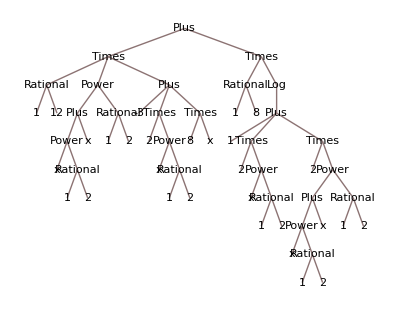

```mathematica
TreeForm[expr]
```

```mathematica
Depth[expr]
```

9

```mathematica
DeleteCases[expr,Sqrt[_],{4}]
```

1/12 √x (-1+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
DeleteCases[expr,Sqrt[_],4]
```

1/12 (-1+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

```mathematica
DeleteCases[expr,Sqrt[_],Infinity]
```

1/12 (-1+8 x)+Log[5]/8

Предварительная обработка данных

```mathematica
signal=Import["collectorData.dat","List"]; (*все лежит в моих файлах*)
```

```mathematica
Take[signal,5062;;5080]
```

```mathematica
badvals=Count[signal,_String]
```

```mathematica
Count[signal,Except[_?NumericQ]]
```

```mathematica
Position[signal,_String]
```

1. Из списка натуральных чисел выбрать только те, которые делятся на 2 или 3 или 5.

2. Напишите функцию, которая работает только с натуральными числами и возвращает n/2, если n - четное число, и (3 n+1), если n - нечетное.

3. Напишите функцию, которая вычисляет модуль вещественных и комплексных чисел.

### Transformation rules

ReplaceAll[expr, pattern → replacement]

expr /. pattern → replacement - замена по правилу

```mathematica
x+y/.y->α
```

x+α

```mathematica
ReplaceAll[x+y,y->α]
```

x+α

```mathematica
{a,a}/.a->RandomReal[]
```

{0.241135,0.241135}

```mathematica
Trace[{a,a+a}/.a->RandomReal[]]
```

{{{a+a,2 a},{a,2 a}},{{RandomReal[],0.772726},a→0.772726,a→0.772726},{a,2 a}/.a→0.772726,{0.772726,2 0.772726},{2 0.772726,1.54545},{0.772726,1.54545}}

```mathematica
{a,a}/.a :>RandomReal[] (*Esc :> Esc отложенная замена*)
```

{0.0515279,0.838185}

```mathematica
Trace[{a,a}/.a :>RandomReal[] ]
```

{{a:>RandomReal[],a:>RandomReal[]},{a,a}/.a:>RandomReal[],{RandomReal[],RandomReal[]},{RandomReal[],0.918457},{RandomReal[],0.0339764},{0.918457,0.0339764}}

```mathematica
{a,b,c}/.List->Plus (*заменили "голову"*)
```

a+b+c

```mathematica
mat={{a,b,c},{d,e,f}};
```

```mathematica
MatrixForm[mat]
```

(a | b | c
d | e | f)

```mathematica
(*переставим столбцы*)
```

```mathematica
mat/.{col1_,col2_,col3_} :>{col1,col3,col2}//MatrixForm
```

(a | c | b
d | f | e)

```mathematica
(*заменим диагональные элементы*)
```

```mathematica
ReplacePart[mat,{i_,i_}->0]//MatrixForm
```

(0 | b | c
d | 0 | f)

```mathematica
{a,b,c}/.{c:> b,b:> a} (*правила применяются только один раз*)
```

{a,a,b}

```mathematica
{a,b,c}//.{c:> b,b:> a} (*правила применяются пока возможно*)
```

{a,a,a}

```mathematica
a b c d/.x_ y_ :>x+y
```

a+b c d

```mathematica
a b c d//.x_ y_:> x+y
```

a+b+c+d

```mathematica
{{x1,y1},{x2,y2},{x3,y3},x4,y4}/.{x_,y_} :>x+y (*вместо списка из 2х элементов - сумма элементов*)
```

{x1+y1,x2+y2,x3+y3,x4,y4}

```mathematica
(*отразим график относительно прямой y = x*)
```

```mathematica
gr=Plot[Sin[x],{x,0,2 π}];
```

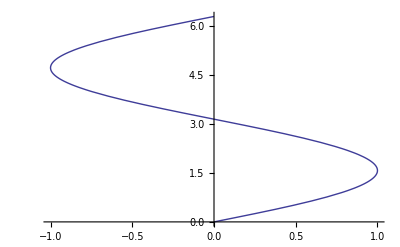

```mathematica
gr/.{x_?NumberQ,y_?NumberQ} :>{y,x}
```

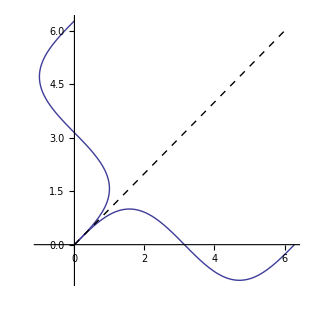

```mathematica
Show[{gr,gr/.{x_?NumberQ,y_?NumberQ} :>{y,x},Graphics[{Dashed,Line[{{0,0},{6,6}}]}]},PlotRange->All,AspectRatio->Automatic] (*plotrangeall !*)
```

```mathematica
(*Замены можно делать, где угодно*)
```

```mathematica
StringReplace["acgttttccctgagcataaaaacccagcaatacg",{"ca"->"CA","tt"->"TT"}]
```

acgTTTTccctgagCAtaaaaaccCAgCAatacg

```mathematica
RandomReal[1,{3,3}]
```

{{0.289866,0.426779,0.582289},{0.211237,0.447899,0.485708},{0.207748,0.0381586,0.512884}}

```mathematica
{{0.2898,0.42677,"NAN"},{0.2112,0.4479,0.4857},{0.2077,"NAN",0.5129}}/.(_String->0.0)
```

{{0.2898,0.42677,0.},{0.2112,0.4479,0.4857},{0.2077,0.,0.5129}}

```mathematica
lis={f,12,"64",0.5,{a,b,c},-0.2,π};
```

```mathematica
Cases[lis,n_?NumericQ:> n^2]
```

{144,0.25,0.04,π^2}

4. С помощью паттернов получите только отрицательные вещественные корни следующего полинома
x^9 + 3.4 x^6 - 25 x^5 - 213 x^4 - 477 x^3 + 1012 x^2 + 111 x - 123

5. Напишите правило, которое делает список одномерным  (заменяет вложенные списки на последовательность из  элементов)

{{α, α, α}, {α}, {{β, γ, β}, {β, β}}, {α, α}} - >
{α, α, α, α, β, γ, β, β, β, α, α}

### Фильтрация данных

```mathematica
sig=Import["signal.dat","List"];
```

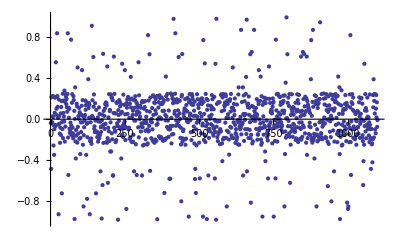

```mathematica
ListPlot[sig,PlotRange->{-1,1}]
```

```mathematica
(* только данные из промежутка*)
```

```mathematica
filtered=Cases[sig,p_/;-0.3<p<0.3];
```

```mathematica
ListPlot[filtered,PlotRange->{-1,1}]
```

ListPlot::nonopt: Options expected (instead of PlotRange → {-1, 1}) beyond position 1 in ListPlot[{-0.0387437, 0.212814, -0.0305973, « 45 », 0.115259, 0.072618, « 919 »}, PlotRange → {« 1 »}]. An option must be a rule or a list of rules.

ListPlot[{-0.0387437,0.212814,-0.0305973,-0.0405029,-0.0296645,0.027855,0.226271,0.0207665,-0.256265,-0.0598483,-0.0971133,0.0622912,0.208881,-0.0694115,-0.0572413,0.0435075,0.101537,0.220481,0.224891,0.120045,0.0137286,-0.0529588,0.191045,0.027855,-0.0443928,-0.14029,-0.229684,-0.0826558,0.0563754,-0.154063,0.118311,0.175705,-0.0266796,-0.0961616,0.247886,-0.184458,0.0604642,0.181485,0.0266683,-0.0223492,0.27836,-0.217994,0.167227,-0.0713868,0.243342,0.220172,0.146534,0.195819,0.115259,0.072618,0.245432,-0.178817,0.112062,0.0139554,0.0997867,-0.0913887,-0.133803,-0.10921,-0.0331438,-0.142767,-0.061637,-0.154454,0.159301,0.243837,-0.0829072,-0.135999,-0.185557,0.223405,0.186045,-0.154454,0.0807537,0.00320578,-0.216336,-0.104622,-0.159802,0.150789,0.125076,-0.228308,-0.0752692,-0.14029,0.0317259,0.00358898,0.108865,-0.190855,0.0670562,0.0563754,-0.181587,-0.0305973,-0.124942,0.0414766,0.130409,-0.0305973,0.185494,-0.249164,0.027539,-0.156061,-0.0785324,0.0225374,-0.0141179,0.0415902,0.181073,0.0912182,0.134852,0.165601,-0.0455662,-0.175494,0.146723,-0.0341163,0.108434,0.157758,0.0152646,0.139348,-0.213152,-0.193057,-0.0295404,-0.213806,-0.187539,-0.239244,0.0317259,0.18401,0.01237,0.0139554,0.120799,0.240594,-0.093541,-0.0694115,-0.126501,0.154651,-0.0135288,-0.119472,0.0905758,-0.00497004,-0.121022,-0.174283,-0.133803,0.0171906,-0.21814,-0.0216631,-0.189731,0.115259,-0.185557,0.0512241,-0.156061,-0.0253562,-0.0795618,-0.124942,-0.0713868,-0.0089212,0.0436359,-0.064181,-0.23099,0.0808759,-0.0514731,0.0314466,-0.0947716,0.104106,0.146534,-0.0455662,0.162865,-0.223682,0.157758,0.134044,-0.229684,-0.184934,-0.0829072,0.0171906,-0.117134,0.243539,-0.212273,0.0786846,0.0905758,-0.03049,0.24054,0.210729,-0.137446,0.208881,-0.195797,0.18401,0.0607075,-0.0832778,0.246209,0.0563754,-0.111885,-0.122357,-0.223682,0.0563754,-0.203478,0.16447,0.156389,-0.0403307,-0.0663526,-0.0651489,0.0878869,0.0401506,-0.016301,0.186013,-0.0795618,0.168791,0.124807,-0.0947283,0.0535926,0.14569,-0.15843,0.0715754,-0.152518,-0.061637,-0.174283,0.238787,-0.0873642,-0.0420276,0.139348,-0.0223492,0.0475923,-0.203094,-0.0752692,0.14569,0.158391,0.111688,0.192732,0.0519164,0.146534,0.217457,-0.100127,0.148766,-0.0826558,0.0139554,-0.19112,0.151591,0.191045,-0.175852,0.113588,-0.218435,0.200525,0.01237,-0.223343,0.0409678,0.0825968,-0.219603,-0.151028,0.185494,-0.0135288,0.111001,0.186045,0.223647,-0.0125107,-0.243906,0.0437078,0.163995,0.0715754,0.142777,0.0779861,0.118042,-0.0795618,-0.176567,0.232215,0.0616483,0.00162801,0.0253965,0.128677,0.112062,-0.119472,-0.0713868,-0.0408348,0.163443,0.177157,-0.0785324,-0.256265,0.167227,-0.0397938,0.101537,-0.248521,-0.0163354,0.118311,0.175705,-0.113446,-0.195043,-0.0192311,0.0245942,-0.0387437,0.0808759,-0.246628,-0.100127,-0.23596,-0.119472,0.181231,-0.113446,-0.0651489,0.072618,0.210729,-0.0125107,-0.0216631,-0.184934,0.00257198,-0.0305273,0.108961,-0.0984601,-0.211063,0.232215,0.0414766,-0.218734,0.220481,0.162187,-0.229684,0.156507,-0.198,0.0854971,0.195819,0.0519164,-0.211682,-0.0554015,0.226289,-0.045793,-0.00497004,0.00162801,0.113588,0.165601,-0.16755,0.0164934,0.232294,0.205898,-0.185694,0.0141415,0.14771,-0.174283,0.00162801,0.210729,0.156937,0.148767,0.0800045,-0.203478,-0.211063,0.168292,0.186013,0.0813098,-0.192403,-0.203094,0.0414766,-0.0117666,0.223647,0.0266683,-0.183465,-0.0752692,0.245733,0.191045,-0.0134792,-0.0947716,-0.172362,0.0839132,-0.099165,-0.0975221,-0.0975567,-0.066334,0.250398,0.01237,-0.23596,-0.149279,0.230589,0.200132,-0.0651489,0.156389,-0.144817,0.168292,0.191045,0.0535926,0.0786846,0.247886,0.164477,-0.064181,-0.0134792,0.0314466,0.194517,-0.0514731,0.16447,0.0342772,0.0854971,-0.0206666,0.18401,-0.0663526,0.0562089,0.1788,0.00257198,-0.181343,-0.0826558,-0.246628,0.220481,0.236215,-0.218435,-0.187539,-0.117134,-0.100127,0.0519164,0.0225374,0.0807537,0.104412,-0.196316,0.195166,-0.24929,0.0878869,-0.189731,0.138596,0.000286803,-0.0206666,0.0743359,0.208881,-0.000911241,-0.0291497,-0.018815,0.166354,0.186013,0.244189,0.0331159,0.0535926,-0.00787337,-0.126501,0.156507,-0.203094,0.142999,0.243342,0.226271,0.197288,-0.121022,0.139189,0.0317259,-0.0713868,0.0824444,-0.23655,0.170752,0.0331159,-0.0984601,-0.255158,-0.0346092,0.243342,0.0240606,0.194517,-0.0163354,0.139348,0.108434,0.142777,-0.228813,-0.0125107,0.0607075,0.181485,0.162865,-0.13687,0.199707,0.0266683,0.14771,0.202046,-0.061637,-0.0422547,0.168292,-0.201983,0.0512241,-0.150517,-0.163878,-0.22284,0.245733,-0.0685344,-0.0132841,0.197288,0.0912182,-0.045793,0.186045,0.134044,-0.0961612,-0.181872,0.027855,-0.0947716,-0.119629,0.00320578,0.01237,0.129917,-0.0491064,0.0954045,0.0429661,0.234342,0.111001,0.194517,-0.0651489,-0.137751,-0.159826,0.0963104,-0.0939326,0.217457,-0.00585167,-0.124942,-0.018815,-0.0729401,0.148767,-0.175494,-0.0225396,-0.213806,0.163443,-0.143354,0.163995,-0.122305,-0.018815,0.164832,-0.243906,-0.0971133,-0.112485,-0.119472,0.233885,0.242867,0.0777111,-0.236021,0.211046,-0.198,0.23885,0.242867,-0.181587,0.0878869,0.136648,0.125076,0.162865,-0.0341163,0.240822,0.224473,-0.182738,0.013457,-0.112485,0.181231,0.14771,0.0475923,0.012638,-0.126501,-0.198,0.181231,0.177157,0.195166,-0.0752692,0.0743359,0.245733,-0.0829072,-0.158082,0.111688,-0.181587,0.012638,0.108434,-0.183465,-0.0305273,0.148767,0.0839132,0.0401506,0.202046,-0.0554473,-0.23099,-0.135999,-0.0971133,-0.150517,-0.201983,0.142999,-0.175852,-0.018815,-0.00887685,-0.245045,0.240594,-0.0346092,-0.248745,-0.0735752,-0.00887685,-0.0975567,0.0240606,-0.0832778,-0.147833,-0.0572413,0.167227,-0.0405029,-0.0341163,0.0505799,0.230589,-0.211682,0.036882,0.174323,-0.00559078,-0.0975567,0.0509421,0.246209,-0.144695,0.146723,-0.0971133,0.118311,0.151591,-0.183465,0.220601,0.0415902,0.111688,-0.1039,-0.0291497,-0.185694,-0.152518,0.0240606,0.128677,-0.23596,0.0225374,-0.216336,-0.00787337,0.118311,-0.0132841,0.0777111,0.0101575,0.036882,-0.0163354,0.0562089,0.108708,-0.0947283,0.0208871,0.195166,0.043911,-0.200016,-0.147833,-0.151028,0.177157,0.146723,-0.110261,-0.00208482,-0.0860614,0.1788,-0.0420276,-0.198,-0.249164,0.223405,-0.229684,-0.0873642,0.139189,-0.0303309,0.027539,-0.151028,0.168292,0.208881,-0.064181,-0.0785324,0.156389,0.199707,0.199707,-0.0132841,-0.137751,-0.175852,-0.111657,-0.208131,-0.149717,-0.0663526,0.198091,-0.0528637,-0.0860614,0.1579,-0.0291497,0.0670562,0.0893159,0.073649,0.0854971,0.0563754,-0.236021,0.120799,0.202046,0.158391,0.168292,-0.0826558,-0.0596933,-0.00559078,-0.212273,-0.0117666,-0.0785324,0.0854971,0.242708,0.0266683,-0.218058,-0.0422547,0.246209,0.00162801,-0.0693517,0.0622144,0.223647,-0.0303309,-0.000911241,0.215593,0.0437078,0.139348,0.165601,-0.0291497,-0.0785324,-0.111885,-0.0598483,0.0825968,0.156507,-0.126501,0.228675,0.177983,0.058607,0.082258,0.231029,-0.119472,-0.180016,0.00579557,-0.159802,0.0101575,0.159301,-0.0685344,0.210729,-0.016301,0.128677,-0.137751,0.244205,-0.171385,-0.0692519,-0.248521,0.0414392,-0.119629,0.104061,0.24229,0.0743359,-0.0956977,-0.171385,0.118042,-0.045793,0.043911,-0.0554015,0.105288,-0.0939326,-0.124942,-0.119477,0.159301,-0.203478,-0.186303,0.0739087,0.00950108,-0.0785324,0.24229,0.0912182,0.186013,-0.22284,0.154876,-0.203478,0.236215,-0.0327808,-0.0826558,0.073649,-0.189258,0.027539,-0.0947716,-0.19836,-0.0305973,0.0813098,-0.172362,0.0429661,-0.061637,0.195772,-0.0785324,0.0409678,0.124807,-0.137751,0.218592,0.0715754,0.0779861,-0.228813,0.200525,0.176521,-0.184458,0.139348,0.118042,0.108865,-0.144817,0.0893159,-0.0693517,-0.0341163,0.0607075,-0.154063,-0.0785324,-0.203094,0.0331159,-0.181343,-0.228308,0.168292,0.120799,-0.203478,-0.180016,-0.142767,0.232215,-0.0545513,-0.158082,0.14771,0.224891,0.180737,-0.149717,-0.0984601,-0.216336,0.108865,0.146534,-0.204241,0.156975,-0.171385,0.197288,-0.0303309,0.195819,-0.187539,-0.0216631,-0.135999,-0.144695,0.244189,-0.183416,-0.195797,-0.0729401,-0.0206666,-0.0572413,-0.0370118,0.250398,0.199707,0.0164934,0.142777,-0.0420276,-0.175852,0.204508,-0.183465,-0.178817,0.243342,0.0878869,0.130409,-0.00559078,-0.218058,0.0703396,0.223405,-0.240876,0.00320578,0.134852,0.0967905,-0.122357,-0.0206666,0.24229,-0.174283,0.0324908,0.0973506,0.235016,0.00257198,0.194517,0.233885,-0.109885,0.232294,0.0824444,-0.218058,0.105288,0.166354,0.181231,0.244189,-0.0554723,0.217457,0.013457,0.162187,-0.144817,-0.223693,0.226289,-0.122305,-0.0422547,0.146534,0.051638,-0.112485,-0.172362,-0.159802,0.134044,0.280952,-0.256265,-0.0545513,-0.248234,0.051638,0.0807537,-0.122357,0.0971074,-0.0225396,0.0967905,-0.0729401,-0.154063,0.14771,0.234342,0.0971074,-0.0956977,-0.213806,0.157758,0.134044,0.127917,-0.0468116,-0.0514731,-0.144817,-0.223693,-0.0832778,0.24054,0.115259,-0.22284,-0.0206666,0.164832,-0.0984601,0.244189,0.148766,0.0912182,0.211046,-0.181872,-0.0713868,0.0777111,-0.0947716,-0.0947283,-0.195797,-0.185557,0.0498565,-0.00497004,-0.156061,-0.249164,-0.0192311,-0.144695,0.073649,0.0793396,-0.0767678,-0.0785324,-0.140245,0.0622912,0.164477,0.212814,0.0240606,-0.181872,-0.045793,-0.0253562,0.0519164,0.199707,0.205898,-0.00171629,-0.178817,0.150789,-0.156061,-0.213806,-0.016301,-0.248234,-0.0676706,0.0854971,0.244189,-0.119472,0.108434,-0.186303,0.082258,0.0077671,-0.0514731,0.210729,0.0245942,-0.0961612,-0.0829072,0.0168856,-0.158082,-0.0305973,-0.223343,0.240594,-0.0554723,-0.192403,-0.0975567,-0.184934,-0.0947716,-0.245045,-0.23655,-0.196316,0.234781,0.115259,-0.178477,0.177983,0.246209,0.0552291,-0.099165,0.242708,-0.13687,0.102475,0.235016,0.0171906,0.164477,-0.0752692,-0.0089212},PlotRange→{-1,1}]

```mathematica
(**)
```

```mathematica
resData=Import["CAresevoir.csv","CSV"]
```

{{Resevoir,Capacity 1000 AF,Hist Avg,2014 AF,2015 AF,% Avg},{UPPER KLAMATH,515.6,341.1,195.7,281.7,83},{CLEAR LAKE,526.8,221,33.2,31.2,14},{GERBER,94.7,48.,2.,1.9,4},{SHASTA DWINNELL,50,21,3.,7.1,34},{TRINITY,2447.7,1953.8,865.4,825.,42},{LEWISTON,14.7,13.9,13.9,13.7,99},{PILLSBURY,80.5,62.9,50.1,24.2,38},{MENDOCINO (COYOTE),122.4,70.,38.8,47.9,68},{WARM SPRINGS,381,214,163.2,192.7,90}}

```mathematica
(*только те хранилища со средней емкостью < 75%, выводим только название и %*)
```

```mathematica
Cases[resData,{res_,__,avg_/;avg<75}:> {res,avg}]
```

{{CLEAR LAKE,14},{GERBER,4},{SHASTA DWINNELL,34},{TRINITY,42},{PILLSBURY,38},{MENDOCINO (COYOTE),68}}

### Сортировка списка

Создать правило, которое сортирует список чисел

```mathematica
nums=RandomReal[1,{10}]
```

{0.512712,0.912127,0.0140513,0.0825807,0.879332,0.699382,0.552749,0.277476,0.357036,0.268008}

```mathematica
listSort={{x___,a_?NumericQ,b_?NumericQ,y___} :>{x,b,a,y}/;b<a}; (*возможно что-то есть в начале списка, возможно нет; пузырек*)
```

```mathematica
nums/.listSort
```

{0.512712,0.0140513,0.912127,0.0825807,0.879332,0.699382,0.552749,0.277476,0.357036,0.268008}

```mathematica
%/. listSort
```

{0.0140513,0.512712,0.912127,0.0825807,0.879332,0.699382,0.552749,0.277476,0.357036,0.268008}

```mathematica
nums//.listSort
```

{0.259725,0.269543,0.278128,0.307913,0.802003,0.821957,0.885754,0.976501,0.979497,0.994767}

```mathematica
{ⅇ ,π,EulerGamma,GoldenRatio,1} // N
```

{2.71828,3.14159,0.577216,1.61803,1.}

```mathematica
{ⅇ ,π,EulerGamma,GoldenRatio,1}//.listSort
```

{EulerGamma,1,GoldenRatio,ⅇ,π}

```mathematica
Sort[{ⅇ ,π,EulerGamma,GoldenRatio,1}]
```

```mathematica
{1,ⅇ,EulerGamma,GoldenRatio,π} (*сорт символов и чисел (сначала числа)*)
```

```mathematica
Sort[{ⅇ ,π,EulerGamma,GoldenRatio,1},Greater]
```

{π,ⅇ,GoldenRatio,1,EulerGamma}

```mathematica
Sort[{ⅇ ,π,EulerGamma,GoldenRatio,1},Less]
```

{EulerGamma,1,GoldenRatio,ⅇ,π}